```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/results.csv"];
raw = raw[[2;;]];
```

```mathematica
maxDistance[pts_]:=(
Flatten[Table[
Norm[pt1-pt2],
{pt1, pts},
{pt2,pts}
]]//Max
)
```

```mathematica
data =
{
#[[1]],
ArrayReshape[
#[[2;;]],
{3,2}
]
}&/@raw;

data = {#[[1]],maxDistance[#[[2]]]}&/@data;
```

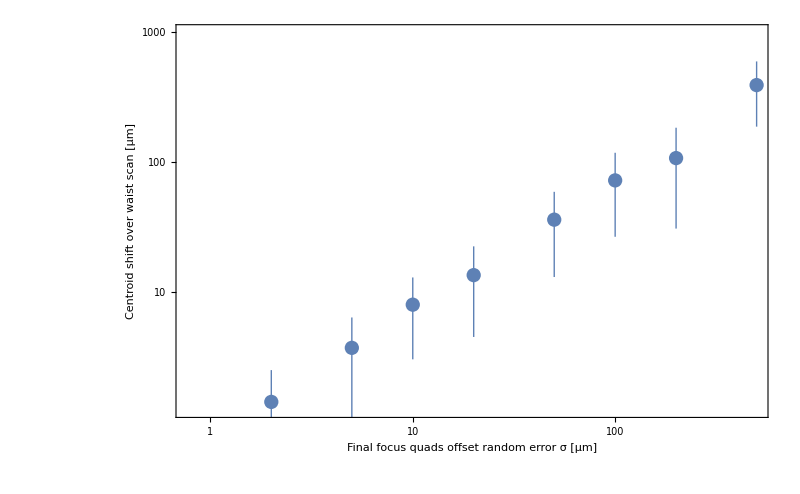

```mathematica
groupedData = GroupBy[data, First];
groupedData=Values[groupedData];
groupedData={#[[1,1]],Around[#[[All,2]]]}&/@groupedData;

ListLogLogPlot[
10^6 groupedData,
ImageSize->800,
PlotRange->{0,1000},
LabelStyle->20,
Frame->True,
FrameLabel->{"Final focus quads offset \n random error σ [μm]", "Centroid shift over waist scan [μm]"}
]
```